```mathematica
(*** Set your directory ***)
(*GetEnvironment[]*)
SetDirectory["/Users/poulh/Box Sync/NTNU/Networking Research Group/Projects/COST Action CA15127 RECODIS/STSM/Poul (Chalmers)/Paper idea"];
<<"StateDiagrams.m"
```

### DRCN 2023: Phased recovery after massive failure

#### From OmNet+ simulations of performance in the (5G/6G) network with slices and HTP.

Input to the simulator : Bottleneck capacity (out of full capacity as in stage 0): ℬ = {b_j} = {1.00, 0.02,0.00, 0.20, 0.50, 0.80} - and traffic type definitations and slice configurations 

Output from simulation: probabilities of non-violations, m_ij (thresholds of throughput or delay), for each slice i for each of the stages j, i.e., with different bottleneck
s_i = {m_(i0,)m_i1, ..., m_iF}, F = number of phases (0 is normal before failure)

#### Read from file

```mathematica
SetDirectory["/Users/poulh/Dropbox/Apps/Overleaf/[DRCN 2023] Survivability Assessment of 5G Network Slicing for Critical Services During Massive Outages/math"]
```

/Users/poulh/Library/CloudStorage/Dropbox/Apps/Overleaf/[DRCN 2023] Survivability Assessment of 5G Network Slicing for Critical Services During Massive Outages/math

```mathematica
(* threshold contains both throughput and delay sensitive sources *)
trace =ReadList["threshold-v4.csv",{String}];
(*trace =
ReadList["/Users/poulh/Dropbox/Apps/Overleaf/[DRCN 2023] Survivability Assessment of 5G Network Slicing for Critical Services During Massive Outages/math/threshold-v3.csv",{String}];*)
(*trace =ReadList["delay-filter.csv",{String}];*)
trace //MatrixForm;
(* Read header? *)
header = StringSplit[trace[[1]],";"][[1]];
(* Remove header? *)
(*trace=Drop[trace,1];*)
(* Convert to table *)
trace1 =StringSplit[trace[[#]],";"][[1]]&/@ Range[Length[trace]];
(* Convert string to numbers *)
trace = ToExpression[trace1];
xx=3;
Take[trace,{2+8(xx-1),9+8(xx-1)}]// MatrixForm;
trace// MatrixForm;
```

#### Mappings between user type and id

```mathematica
ntypes = {"VDI"->1,"LVD"->2,"FDO"->3,"SSH"->4,"VIP"->5,"cVIP"->6,
"cF"->7,"cLV"->8};
ctypes = {1->"VDI",2->"LVD",3->"FDO",4->"SSH",5->"VIP",6->"cVIP",7->"cF",8->"cLV"};
```

#### Mappings between scenario and id

```mathematica
sttypes = {"S3"->"S_(<2c,8>)","S4"->"S_(<2c,2c>)","S5"->"S_(<2c,4c>)","S6"->"S_(<2d,2d>)","S7"->"S_(<4cd,4cd>)","S8"->"S_(<4c,8>)",
"S9"->"S_(<3,4c>)","S10"->"S_(<2c,4cd>)","S11"->"S_(<3,8>)","S12"->"S_(<3,4cd>)"};
idttypes = #[[2]]->#[[1]] & /@ sttypes
stypes = {"S3"->1,"S4"->2,"S5"->3,"S6"->4,"S7"->5,"S8"->6,"S9"->7,"S10"->8,"S11"->9,"S12"->10};
idtypes = #[[2]]->#[[1]] & /@ stypes;
idttypes /. stypes
idtypes /. sttypes
```

{S_(2c,8)→S3,S_(2c,2c)→S4,S_(2c,4c)→S5,S_(2d,2d)→S6,S_(4cd,4cd)→S7,S_(4c,8)→S8,S_(3,4c)→S9,S_(2c,4cd)→S10,S_(3,8)→S11,S_(3,4cd)→S12}

{S_(2c,8)→1,S_(2c,2c)→2,S_(2c,4c)→3,S_(2d,2d)→4,S_(4cd,4cd)→5,S_(4c,8)→6,S_(3,4c)→7,S_(2c,4cd)→8,S_(3,8)→9,S_(3,4cd)→10}

{1→S_(2c,8),2→S_(2c,2c),3→S_(2c,4c),4→S_(2d,2d),5→S_(4cd,4cd),6→S_(4c,8),7→S_(3,4c),8→S_(2c,4cd),9→S_(3,8),10→S_(3,4cd)}

```mathematica
Subscript[𝒮, 8,10]
```

𝒮_(8,10)

#### Select user type (k) and slice configuration (i)

```mathematica
Subscript[𝒜, i_]:=Take[trace,{2+8*(i-1),9+8*(i-1)}];
(* Delete 5% -> 2, 10% -> 3, 20% -> 4, 30% -> 5*)
Subscript[𝒮, k_,i_]:= (#[[k+5]]&/@Delete[Subscript[𝒜, i],{5}]);
(* Example of use: print the performance of the stages for "cLV" in scenario 1-5 *)
Subscript[𝒮, "cLV"/.ntypes,#]& /@ {1,2,3,4,5,10} //MatrixForm
(* Example of use: print the performance of the delay sensitive in scenario 1 *)
Subscript[𝒮, #,1]& /@ {5,6} //MatrixForm
```

(0. | 22.2 | 0. | 100 | 0. | 0. | 0.
0 | 100 | 16.67 | 100 | 0. | 0. | 0.
0 | 27.8 | 0 | 100 | 0. | 0. | 0.
0. | 100 | 100 | 100 | 100 | 100 | 11.11
0. | 100 | 16.67 | 100 | 0. | 0. | 0.
0 | 100 | 22.2 | 100 | 0 | 0 | 0)

(0 | 97.67 | 96.01 | 100 | 95.71 | 38.94 | 0
0. | 55.155 | 0 | 100 | 0 | 0 | 0)

#### Disaster model

Stage 0: Normal situation before disaster
Stage 1: Disaster hits, rerouting possible but with very limited capacity (5% /10%)
Stage 2: With q_1 the seconday effect of disaster kicks in and all communications (slices) are disconnected (0%)
Stage 3: Emergency base station (e.g.Airborne) is installed and a reduced capacity reestablished, main focus on high priority, critical services (20%)
Stage 4: Second step to reestablish services, more capacity for all services (30%)
Stage 5: Thrid step to reestablish services,even more full capacity for all services (40%)
Stage 6: Last step to reestablish services,close to full capacity for all services (80%)
-Graphics-

#### Build set of equations

```mathematica
(* Six stages (Subscript[𝒩, p]=6) - each stage j can be non-exponential (here Erlang-Subscript[k, j])*)
(* Erlang-k(k*Subscript[μ, i]) for phase i=1-6 (0<=k<10) - Subscript[k, i]=0 is n.e.d. *)
(* Note that this means that the the stage i is modelled by Subscript[k, i]+1 substates, i*10+l, l=0,...,Subscript[k, i] *)
Subscript[𝒩, c]=8;
Subscript[𝒩, p]=6;
Subscript[𝒮, 0,i_]:=δ;
Subscript[k, 1]=2;
Subscript[k, 2]=9;
Subscript[k, 3]=9;
Subscript[k, 4]=3;
Subscript[k, 5]=3;
Subscript[k, 6]=3;
eq={Subscript[p, 10]'[t]== -Subscript[μ, 1] Subscript[p, 10][t]};
AppendTo[eq,Subscript[p, 10+#+1]'[t]== -Subscript[μ, 1] Subscript[p, 10+#+1][t]+Subscript[μ, 1] Subscript[p, 10+#][t]&/@Range[0,Subscript[k, 1]-1]];

(* Subscript[q, 1] is the probabilty of secondary effect of the dister before establishment of a stable connection for emergency comm. *) 
AppendTo[eq,Subscript[p, 20]'[t]==Subscript[μ, 1] Subscript[q, 1] Subscript[p, 10+Subscript[k, 1]][t]-Subscript[μ, 2] Subscript[p, 20][t]];
AppendTo[eq,Subscript[p, 20+#+1]'[t]== -Subscript[μ, 2] Subscript[p, 20+#+1][t]+Subscript[μ, 2] Subscript[p, 20+#][t] &/@ Range[0,Subscript[k, 2]-1]];

AppendTo[eq,Subscript[p, 30]'[t]==Subscript[μ, 1] (1-Subscript[q, 1]) Subscript[p, 10+Subscript[k, 1]][t] + Subscript[μ, 2] Subscript[p, 20+Subscript[k, 2]][t]-Subscript[μ, 3] Subscript[p, 30][t]];
AppendTo[eq,Subscript[p, 30+#+1]'[t]== -Subscript[μ, 3] Subscript[p, 30+#+1][t]+Subscript[μ, 3] Subscript[p, 30+#][t] &/@ Range[0,Subscript[k, 3]-1]];

AppendTo[eq,Subscript[p, 40]'[t]==Subscript[μ, 3] Subscript[p, 30+Subscript[k, 3]][t]-Subscript[μ, 4] Subscript[p, 40][t]];
AppendTo[eq,Subscript[p, 40+#+1]'[t]== -Subscript[μ, 4] Subscript[p, 40+#+1][t]+Subscript[μ, 4] Subscript[p, 40+#][t] &/@ Range[0,Subscript[k, 4]-1]];

AppendTo[eq,Subscript[p, 50]'[t]==Subscript[μ, 4] Subscript[p, 40+Subscript[k, 4]][t]-Subscript[μ, 5] Subscript[p, 50][t]];
AppendTo[eq,Subscript[p, 50+#+1]'[t]== -Subscript[μ, 5] Subscript[p, 50+#+1][t]+Subscript[μ, 5] Subscript[p, 50+#][t] &/@ Range[0,Subscript[k, 5]-1]];

AppendTo[eq,Subscript[p, 60]'[t]==Subscript[μ, 5] Subscript[p, 50+Subscript[k, 5]][t]-Subscript[μ, 6] Subscript[p, 60][t]];
AppendTo[eq,Subscript[p, 60+#+1]'[t]== -Subscript[μ, 6] Subscript[p, 60+#+1][t]+Subscript[μ, 6] Subscript[p, 60+#][t] &/@ Range[0,Subscript[k, 6]-1]];

AppendTo[eq,Subscript[p, 0]'[t]==Subscript[μ, 6] Subscript[p, 60+Subscript[k, 6]][t]];
eq = Flatten[eq];
eq //MatrixForm;
(* variables are the transient probabilites of state i *) 
vars = {
	Subscript[p, 10+#][t] &/@ Range[0,Subscript[k, 1]],
	Subscript[p, 20+#][t] &/@ Range[0,Subscript[k, 2]],
	Subscript[p, 30+#][t] &/@ Range[0,Subscript[k, 3]],
	Subscript[p, 40+#][t] &/@ Range[0,Subscript[k, 4]],
	Subscript[p, 50+#][t] &/@ Range[0,Subscript[k, 5]],
	Subscript[p, 60+#][t] &/@ Range[0,Subscript[k, 6]],
	Subscript[p, 0][t]} //Flatten;
(* Initial value of the variables *) 
init ={
	Subscript[p, 10][0]==1,(Subscript[p, 10+#][0]==0) &/@ Range[1,Subscript[k, 1]],
	(Subscript[p, 20+#][0]==0) &/@ Range[0,Subscript[k, 2]],
	(Subscript[p, 30+#][0]==0) &/@ Range[0,Subscript[k, 3]],
	(Subscript[p, 40+#][0]==0) &/@ Range[0,Subscript[k, 4]],
	(Subscript[p, 50+#][0]==0) &/@ Range[0,Subscript[k, 5]],
	(Subscript[p, 60+#][0]==0) &/@ Range[0,Subscript[k, 6]],
	Subscript[p, 0][0]==0} //Flatten;
(* Parameters: rates = 1/expected duration of stages *)
para={
	Subscript[q, 1]->0.7,
	Subscript[μ, 1]->(Subscript[k, 1]+1)/(1*60),
	Subscript[μ, 2]->(Subscript[k, 2]+1)/(8*60),
	Subscript[μ, 3]->(Subscript[k, 3]+1)/(1*24*60),
	Subscript[μ, 4]->(Subscript[k, 4]+1)/(3*24*60),
	Subscript[μ, 5]->(Subscript[k, 5]+1)/(7*24*60),
	Subscript[μ, 6]->(Subscript[k, 6]+1)/(14*24*60)};
eq /.para //MatrixForm;
(* Reward (probablity to not violating the agreement, 
	i.e., either lower bounds in thoughput, or upper bound on delay) *)
(* Ex with eight slices - 5 non-critical (1-5), 3 critical(6-8) *)
(* {1->"VDI",2->"LVD",3->"FDO",4->"SSH",5->"VIP",6->"cVP",7->"cF",8->"cLV"} *)
(* Parameters data for simulations: bw constraints on bottleneck *)
(* Stage I   :  2% of C *)
(* Stage II  :  0% of C - totally disconnected *)
(* Stage III : 20% of C *)
(* Stage IV  : 50% of C *)
(* Stage V   : 80% of C *)
```

#### Solve

```mathematica
(* Solve *)
sol=NDSolve[Flatten[{(eq /.para),init}],vars,{t,0,200000}] //Simplify;
Subscript[f, 0][t_] = Subscript[p, 0][t] /. sol[[1]];
Subscript[f, 1][t_]= Apply[Plus,(Subscript[p, 10+#][t] /. sol[[1]])&/@Range[0,Subscript[k, 1]]];
Subscript[f, 2][t_]= Apply[Plus,(Subscript[p, 20+#][t] /. sol[[1]])&/@Range[0,Subscript[k, 2]]];
Subscript[f, 3][t_]= Apply[Plus,(Subscript[p, 30+#][t] /. sol[[1]])&/@Range[0,Subscript[k, 3]]];
Subscript[f, 4][t_]= Apply[Plus,(Subscript[p, 40+#][t] /. sol[[1]])&/@Range[0,Subscript[k, 4]]];
Subscript[f, 5][t_]= Apply[Plus,(Subscript[p, 50+#][t] /. sol[[1]])&/@Range[0,Subscript[k, 5]]];
Subscript[f, 6][t_]= Apply[Plus,(Subscript[p, 60+#][t] /. sol[[1]])&/@Range[0,Subscript[k, 6]]];
F[t_]:=Table[Subscript[f, i][t],{i,0,Subscript[𝒩, p]}];
(Subscript[H, #][t_,i_]:=F[t].Subscript[𝒮, #,i] /. para) &/@ Range[Subscript[𝒩, c]];
(Subscript[X, #][t_,i_]:=If[(t<0),Subscript[𝒮, #,i][[1]],Subscript[H, #][t,i]]) &/@ Range[Subscript[𝒩, c]];
```

#### Plot

Define plots

```mathematica
stypes
```

{S3→1,S4→2,S5→3,S6→4,S7→5,S8→6,S9→7,S10→8,S11→9,S12→10}

```mathematica
(* No of plots *)
Ns=4;
(* Compare 1: critical VoIP (cVIP), critical/non-critical pri, different slicing *)
Subscript[χ, 1] = {"S3","S4","S5","S6","S10"} /. stypes;
Subscript[U, 1]={"cVIP"} /. ntypes;
Subscript[u, 1]=5000;
Subscript[x, 1]=0.9;
Subscript[y, 1]=0.5;

(* Compare 2: non-critical file download (FDO), critical/non-critical pri, different slicing *)
Subscript[χ, 2] = Subscript[χ, 1];
Subscript[U, 2]={"FDO"} /. ntypes;
Subscript[u, 2]=30000;
Subscript[x, 2]=0.9;
Subscript[y, 2]=0.35;

(* Compare 3: critical Live Video (cLV), critical/non-critical pri, different slicing *)
Subscript[χ, 3] = Subscript[χ, 1];
Subscript[U, 3]={"cLV"} /. ntypes;
Subscript[u, 3]=30000;
Subscript[x, 3]=0.85;
Subscript[y, 3]=0.6;

(* Compare 4: non-critical Live Video (LVD), critical/non-critical pri, different slicing *)
Subscript[χ, 4] = Subscript[χ, 1];
Subscript[U, 4]={"VIP"} /. ntypes;
Subscript[u, 4]=30000;
Subscript[x, 4]=0.9;
Subscript[y, 4]=0.6;

(* Compare 5: critical VoIP (cVIP), 4 slices (4cd) and different priorities *)
Subscript[χ, 5] = {"S7","S10","S12"} /. stypes;
Subscript[U, 5]=Subscript[U, 1];
Subscript[u, 5]=Subscript[u, 1];
Subscript[x, 5]=0.8;
Subscript[y, 5]=0.8;

(* Compare 6: critical/non-critical Live Video (cLV,LVD), 4 slices (4cd) and different priorities *)
Subscript[χ, 6] = Subscript[χ, 5];
Subscript[U, 6]=Subscript[U, 2];
Subscript[u, 6]=Subscript[u, 2];
Subscript[x, 6]=0.8;
Subscript[y, 6]=0.8;

(* Compare 7: video on demand (VDI), 4 slices (4cd) and different priorities *)
Subscript[χ, 7] = Subscript[χ, 5];
Subscript[U, 7]=Subscript[U, 3];
(*Subscript[u, 7]=Subscript[u, 3];*)
Subscript[u, 7]=5000;
Subscript[x, 7]=0.6;
Subscript[y, 7]=0.6;

(* Compare 8: file download (FDO), 4 slices (4cd) and different priorities *)
Subscript[χ, 8] = Subscript[χ, 5];
Subscript[U, 8]=Subscript[U, 4];
Subscript[u, 8]=Subscript[u, 4];
Subscript[x, 8]=0.7;
Subscript[y, 8]=0.6;
(*Subscript[𝒞, c] = {"cVIP"} /.ntypes;*)
Subscript[𝒞, c] = {"VIP","cVIP"} /.ntypes;
```

```mathematica
(* Prepare for plotting *)
(* Table of plots - one per traffic type in 𝒞 *)
Y[t_,i_, 𝒞_] := (Subscript[X, #][t,i]/100) & /@ 𝒞;
(* Coloring scheme *)
(*Subscript[𝒸, c_,i_]:=Hue[1-#/8,0.5,1-1/(1.5*i)]/. {y->#} &/@ c*)
(*Subscript[𝒸, c_,i_]:=Hue[1-#/8,0.5,1-1/(1.5*i)] &/@ c*)
(*col[c_,i_]:=RGBColor[0.5-c/16,1-i/16,1-c/8];*)
(*Subscript[𝒸, c_,i_]:=col[#,i]&/@c;*)
(* Labels *)
(*Subscript[ℓ, c_,i_]:= # Subscript[SC, i]  & /@ (c /.ctypes)*)
(*lidtypes = {1->"#1:",2->"#2:",3->"#3:",4->"#4:",5->"#5:",6->"#6:",7->"#7:",8->"#8:",9->"#9:",10->"#10:"};*)
lidtypes =idtypes /. sttypes
ltype = {1->"Video",2->"Live video",3->"File download",4->"SSH",5->"VoIP",6->"Critical VoIP",7->"Critical File download",8->"Critical Live video"};
Subscript[ℓ, c_,i_]:=(lidtypes[[i,2]]<>" : "<>#) & /@ (c /.ltype);

(* Common for all plots *)
(* Threshold tolerance (5%) *)
δ=0.05;
l=-50;
Subscript[u, 1]=5000;
Do[ 
(Subscript[𝒱, c,#]=Flatten[Y[t,#,Subscript[U, s]]])&/@ Subscript[χ, s];
Γ=Flatten[Subscript[𝒱, c,#]& /@ Subscript[χ, s]];
Subscript[Π, s]=Γ;
Subscript[𝒴, s]=Flatten[Subscript[ℓ, Subscript[U, s],#]& /@ Subscript[χ, s]];
Subscript[𝒮, s] =Plot[Γ,{t,l,Subscript[u, s]}, 
	PlotRange->All,
	(* PlotLegends->Placed[Subscript[𝒴, s],{Subscript[x, s],Subscript[y, s]}],*)
	PlotLegends->Placed[LineLegend[Automatic,Subscript[χ, s]/. idtypes /. sttypes,LegendFunction->"Frame",LegendLabel->(Subscript[U, s] /. ltype)[[1]]],{Subscript[x, s],Subscript[y, s]}],
	AxesLabel->{t,Subscript[M, i][t]}, AxesOrigin->{l,0}, ImageSize->Large];
,{s,1,Ns}]
```

{1→S_(2c,8),2→S_(2c,2c),3→S_(2c,4c),4→S_(2d,2d),5→S_(4cd,4cd),6→S_(4c,8),7→S_(3,4c),8→S_(2c,4cd),9→S_(3,8),10→S_(3,4cd)}

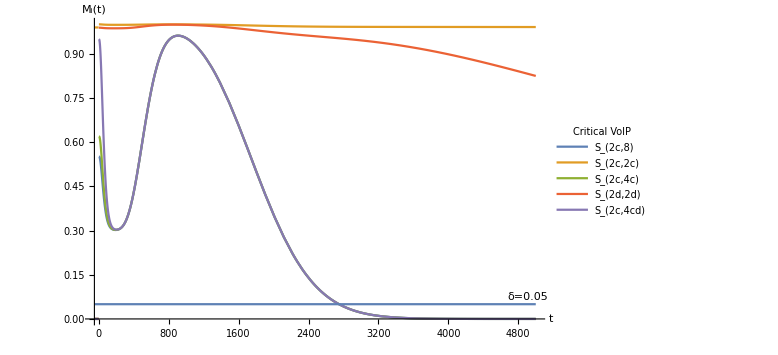
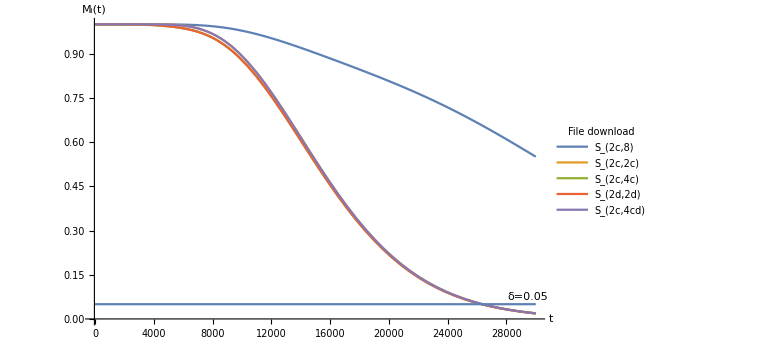
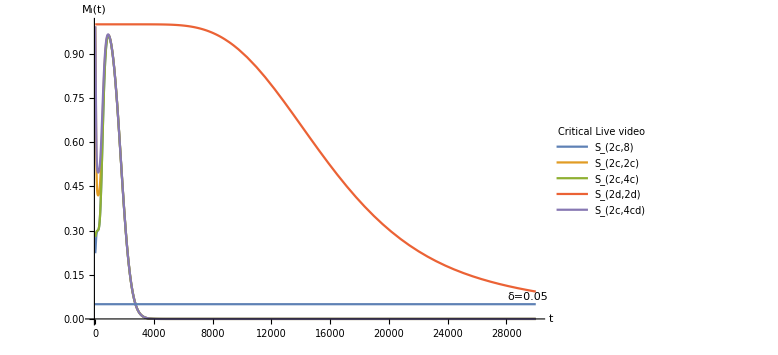
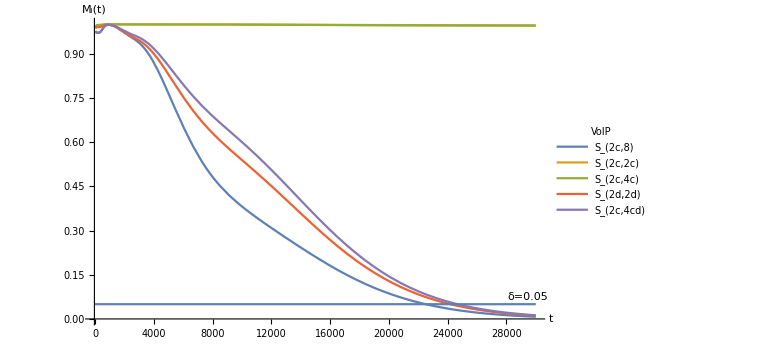

```mathematica
Subscript[plotδ, i_] := Plot[δ,{t,l,Subscript[u, i]},PlotLabels->Placed["δ="<>ToString[δ],Right]];
(Subscript[𝒮, #]=Show[Subscript[𝒮, #],Subscript[plotδ, #] ] )&/@Range[Ns]
```

```mathematica
(* Save all Ns plots *) 
Export["/Users/poulh/Library/CloudStorage/Dropbox/Apps/Overleaf/[DRCN 2023] Survivability Assessment of 5G Network Slicing for Critical Services During Massive Outages/figs/plot"<>ToString[#]<>".pdf",Subscript[𝒮, #]]&/@Range[Ns];
```

#### Find time until threshold τ reached (by FindRoot)

```mathematica
(Subscript[YY, #]=Flatten[Y[t,#,Subscript[U, 1]]])&/@ Subscript[χ, 1];
Γ=Flatten[Subscript[YY, #]& /@ Subscript[χ, 1]]
```

{1/100 If[t<0,𝒮_(6,1)⟦1⟧,H_6[t,1]],1/100 If[t<0,𝒮_(6,2)⟦1⟧,H_6[t,2]],1/100 If[t<0,𝒮_(6,3)⟦1⟧,H_6[t,3]],1/100 If[t<0,𝒮_(6,4)⟦1⟧,H_6[t,4]],1/100 If[t<0,𝒮_(6,8)⟦1⟧,H_6[t,8]]}

```mathematica
Clear[Γ]
```

```mathematica
(Subscript[YY, #]=Flatten[Y[t,#,Subscript[U, 1]]])&/@ Subscript[χ, 1];
 Γ = Flatten[Subscript[YY, #]& /@ Subscript[χ, 1]]
```

{1/100 If[t<0,𝒮_(6,1)⟦1⟧,H_6[t,1]],1/100 If[t<0,𝒮_(6,2)⟦1⟧,H_6[t,2]],1/100 If[t<0,𝒮_(6,3)⟦1⟧,H_6[t,3]],1/100 If[t<0,𝒮_(6,4)⟦1⟧,H_6[t,4]],1/100 If[t<0,𝒮_(6,8)⟦1⟧,H_6[t,8]]}

```mathematica
{Flatten[Subscript[U, #]&/@Range[4]]/.ctypes ,Subscript[χ, 1]/. lidtypes}
```

{{cVIP,FDO,cLV,VIP},{S_(2c,8),S_(2c,2c),S_(2c,4c),S_(2d,2d),S_(2c,4cd)}}

```mathematica
δ=0.05;
(*xx={1,2,3,4,5}
Plot[{δ,Subscript[Π, k][[xx]]},{t,-100,120000},PlotRange->All]*)
roots = {};
k=1;
AppendTo[roots,FindRoot[Subscript[Π, k][[#]]-δ,{t,5000}] &/@ Range[Length[Subscript[Π, k]]] //Flatten];
k=2;
AppendTo[roots,FindRoot[Subscript[Π, k][[#]]-δ,{t,5000}] &/@ Range[Length[Subscript[Π, k]]] //Flatten];
k=3;
AppendTo[roots,FindRoot[Subscript[Π, k][[#]]-δ,{t,5000}] &/@ Range[Length[Subscript[Π, k]]]//Flatten];
k=4;
AppendTo[roots,FindRoot[Subscript[Π, k][[#]]-δ,{t,20000}] &/@ Range[Length[Subscript[Π, k]]]//Flatten];
roots //MatrixForm
tab={};
Do[AppendTo[tab,t /. roots[[i,#]]&/@Range[5]],{i,1,4}]
tab
tab //MatrixForm
TableForm[ tab, TableHeadings->{Flatten[Subscript[U, #]&/@Range[4]]/.ctypes ,Subscript[χ, 1]/. lidtypes} ]
```

InterpolatingFunction::dmval: Input value {605120.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

InterpolatingFunction::dmval: Input value {220010.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

(t→2749.21 | t→192538. | t→2749.21 | t→24072.5 | t→2749.21
t→55602.4 | t→26373.7 | t→26306.8 | t→26306.8 | t→26373.7
t→2749.21 | t→2749.21 | t→2749.21 | t→36971.9 | t→2749.21
t→22502.8 | t→220010. | t→220010. | t→24181.8 | t→24667.)

{{2749.21,192538.,2749.21,24072.5,2749.21},{55602.4,26373.7,26306.8,26306.8,26373.7},{2749.21,2749.21,2749.21,36971.9,2749.21},{22502.8,220010.,220010.,24181.8,24667.}}

(2749.21 | 192538. | 2749.21 | 24072.5 | 2749.21
55602.4 | 26373.7 | 26306.8 | 26306.8 | 26373.7
2749.21 | 2749.21 | 2749.21 | 36971.9 | 2749.21
22502.8 | 220010. | 220010. | 24181.8 | 24667.)

| S_(2c,8) | S_(2c,2c) | S_(2c,4c) | S_(2d,2d) | S_(2c,4cd)
cVIP | 2749.21 | 192538. | 2749.21 | 24072.5 | 2749.21
FDO | 55602.4 | 26373.7 | 26306.8 | 26306.8 | 26373.7
cLV | 2749.21 | 2749.21 | 2749.21 | 36971.9 | 2749.21
VIP | 22502.8 | 220010. | 220010. | 24181.8 | 24667.

```mathematica
Subscript[χ, 1]/. lidtypes
```

{S_(2c,8),S_(2c,2c),S_(2c,4c),S_(2d,2d),S_(2c,4cd)}

```mathematica
Subscript[U, #]/.ctypes &/@Range[Ns]
```

{{cVIP},{FDO},{cLV},{VIP}}

```mathematica
Subscript[χ, 1]
Subscript[χ, 1]/. lidtypes
```

{1,2,3,4,8}

{S_(2c,8),S_(2c,2c),S_(2c,4c),S_(2d,2d),S_(2c,4cd)}

```mathematica
Flatten[Subscript[U, #] /. ltype &/@Range[4]]
```

{Critical VoIP,File download,Critical Live video,VoIP}

```mathematica
ntypes
```

{VDI→1,LVD→2,FDO→3,SSH→4,VIP→5,cVIP→6,cF→7,cLV→8}

```mathematica
Max[δ,Subscript[X, 2][-100,#] (1+δ)] &/@ Range[10]
```

{0.05,0.05,0.05,2.835,0.05,0.05,0.05,0.05,0.05,0.05}

```mathematica
(* Function *)
(*T[i_,c_,δ_,ini_]:=(FindRoot[Subscript[X, #1][t,i]-Max[δ,Subscript[X, #1][-100,i] (1+δ)],{t,ini},AccuracyGoal->6]&)/@c*)
T[i_,c_,δ_,ini_]:=(FindRoot[Subscript[X, #][t,i]-δ ,{t,ini},AccuracyGoal->2]&)/@c
Subscript[W, k_]:= t /. T[k,Subscript[U, k],δ,30000]
(* Threshold*)
δ=0.5;
(* ex: critical service *)
(* k is scenario, Subscript[χ, k] is set of traffic types *) 
(Subscript[U, #]=Range[8]) &/@ Range[10];
tab = Subscript[W, #]&/@  Range[10];
```

InterpolatingFunction::dmval: Input value {253835.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::jsing: Encountered a singular Jacobian at the point {t} = {30000.}. Try perturbing the initial point(s).

FindRoot::jsing: Encountered a singular Jacobian at the point {t} = {-339867.}. Try perturbing the initial point(s).

```mathematica
tab = t /. T[#,Range[8],δ,10000]&/@ Range[10];
TableForm[ tab, TableHeadings->{#[[2]]&/@sttypes,#[[1]]&/@ntypes} ]
```

InterpolatingFunction::dmval: Input value {253493.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::jsing: Encountered a singular Jacobian at the point {t} = {10000.}. Try perturbing the initial point(s).

| VDI | LVD | FDO | SSH | VIP | cVIP | cF | cLV
S_(2c,8) | 18138.2 | 29715.7 | 72732. | 23242.6 | 31412.1 | 10000. | 10000. | 3392.19
S_(2c,2c) | 27262.8 | 65683.2 | 34687.2 | 110010. | 110010. | 110010. | 10000. | 10000.
S_(2c,4c) | 23738.7 | 64976.6 | 34628.9 | 110010. | 110010. | 10000. | 10000. | 3392.19
S_(2d,2d) | 10000. | 177383. | 34628.9 | 33171.5 | 32804.9 | 32712.8 | 34328. | 58233.1
S_(4cd,4cd) | 13593.6 | 64198.6 | 34687.2 | 33917.2 | 33203.1 | 10000. | 10000. | 10000.
S_(4c,8) | 19931.4 | 28791.6 | 72732. | 60088. | 31780.5 | 10000. | 10000. | 3392.19
S_(3,4c) | 26526.5 | 64198.6 | 34687.2 | 110010. | 110010. | 10000. | 10000. | 3392.19
S_(2c,4cd) | 13582. | 63322.6 | 34687.2 | 33761.8 | 33215.9 | 10000. | 10000. | 10000.
S_(3,8) | 13582. | 63322.6 | 34687.2 | 60196.5 | 30509.3 | 10000. | 10000. | 3392.19
S_(3,4cd) | 13605.2 | 64198.6 | 34687.2 | 33950.2 | 33612.8 | 10000. | 10000. | 10000.

```mathematica
tab[[1,4]]="Inf"
TableForm[ tab, TableHeadings->{#[[2]]&/@sttypes,#[[1]]&/@ntypes} ]
```

Inf

| VDI | LVD | FDO | SSH | VIP | cVIP | cF | cLV
S_(2c,8) | 18138.2 | 29715.7 | 72732. | Inf | 31412.1 | 10000. | 10000. | 3392.19
S_(2c,2c) | 27262.8 | 65683.2 | 34687.2 | 110010. | 110010. | 110010. | 10000. | 10000.
S_(2c,4c) | 23738.7 | 64976.6 | 34628.9 | 110010. | 110010. | 10000. | 10000. | 3392.19
S_(2d,2d) | 10000. | 177383. | 34628.9 | 33171.5 | 32804.9 | 32712.8 | 34328. | 58233.1
S_(4cd,4cd) | 13593.6 | 64198.6 | 34687.2 | 33917.2 | 33203.1 | 10000. | 10000. | 10000.
S_(4c,8) | 19931.4 | 28791.6 | 72732. | 60088. | 31780.5 | 10000. | 10000. | 3392.19
S_(3,4c) | 26526.5 | 64198.6 | 34687.2 | 110010. | 110010. | 10000. | 10000. | 3392.19
S_(2c,4cd) | 13582. | 63322.6 | 34687.2 | 33761.8 | 33215.9 | 10000. | 10000. | 10000.
S_(3,8) | 13582. | 63322.6 | 34687.2 | 60196.5 | 30509.3 | 10000. | 10000. | 3392.19
S_(3,4cd) | 13605.2 | 64198.6 | 34687.2 | 33950.2 | 33612.8 | 10000. | 10000. | 10000.

```mathematica
Position[tab, 16817.950364698878]
```

{}

### Examples of customized plots

```mathematica
(*ℳ = Plot[{Subscript[X, 1][t],Subscript[X, 2][t],Subscript[X, 3][t],Subscript[α, c],Subscript[α, a],u[t],v[t],Subscript[s, 1][[1]],Subscript[s, 2][[1]],Subscript[s, 3][[1]]},{t,-1000,15000}, 
		PlotRange->All,
		PlotStyle->{
		Hue[0.6,0.67,1.],
		Hue[0.33,1.,0.62],
		Hue[0.14,1.,0.79],
		{Opacity[0.5],Dotted,Black},
		{Opacity[0.5],Dotted,Black},
		Hue[0.6,0.67,1.],
		Hue[0.33,1.,0.62],
		{Opacity[0.5],Dashed,LightRed},
		{Opacity[0.5],Dashed,LightRed},
		{Opacity[0.5],Dashed,LightRed}},
		(*PlotLegends->Placed[{"Slice 1","Slice 2","Slice 3"},Below],*)
		PlotLabels->{"Slice 1","Slice 2","Slice 3","α_c","α_a"},
		AxesLabel->{t,Subscript[M, i][t]}, AxesOrigin->{-1000,0}
	]*)
	
(* Plot survivability *)
(*ℳ = Plot[{Subscript[X, 1][t],Subscript[X, 2][t],Subscript[X, 3][t],Subscript[s, 1][[1]],Subscript[s, 2][[1]],Subscript[s, 3][[1]]},{t,-1000,15000}, 
		PlotRange->All,
		PlotStyle->{
		Automatic,Automatic,Automatic,
		{Opacity[0.5],Dashed,LightRed},
		{Opacity[0.5],Dashed,LightRed},
		{Opacity[0.5],Dashed,LightRed}},
		(*PlotLegends->Placed[{"Slice 1","Slice 2","Slice 3"},Below],*)
		PlotLabels->{"Slice 1","Slice 2","Slice 3"},
		AxesLabel->{t,Subscript[M, i][t]}, AxesOrigin->{-1000,0}
	]*)
```

### Old stuff

```mathematica
NClients = 3;
NSlices = 3;
slice = {{1},{2},{3}};
ctypes = {1->"Slice 1",2->"Slice 2",3->"Slice 3"};
Subscript[s, 1] = {0.99,0.10,0,0.5,0.9,0.95};
Subscript[s, 2] = {0.95,0.03,0,0.03,0.50,0.80};
Subscript[s, 3] = {0.90,0.05,0,0.05,0.15,0.75};
```

Slices in the use case of the paper
non-critical : VID, LVD, FDO, SSH, VIP
critical: cVP, cF, cLV

-Graphics-

```mathematica
𝒮=1;
Subscript[𝒩, c] = 8;
Subscript[𝒩, s] = 8;
Subscript[𝒩, p]=6 ; 
slice = {{1},{2},{3},{4},{5},{6},{7},{8}};
ctypes = {1->"VDI",2->"LVD",3->"FDO",4->"SSH",5->"VIP",6->"cVIP",7->"cF",8->"cLV"};
(* Subscript[𝒩, c]=8 clients, Subscript[𝒩, s]=8 slices, Subscript[𝒩, p]=6 phases/stages *)
(* Throughput sensitive : {1,2,3,4,7,8}*)
(* Delay sensitive : {5,6}*)
Subscript[s, 1,𝒮] = {0.00,1.00,1.00,1.00,0.97,0.015,0.00};
Subscript[s, 2,𝒮] = {0.00,1.00,1.00,1.00,0.43,0.24,0.00};
Subscript[s, 3,𝒮] = {0.00,1.00,1.00,1.00,1.00,1.00,0.80};
Subscript[s, 4,𝒮] = {0.00,1.00,1.00,1.00,1.00,1.00,0.00};
Subscript[s, 5,𝒮] = {0.38,1.00,1.00,1.00,0.99,0.44,0.40};
Subscript[s, 6,𝒮] = {0.29,1.00,1.00,1.00,0.41,0.37,0.28};
Subscript[s, 7,𝒮] = {0.00,1.00,1.00,0.00,0.00,0.00,0.00};
Subscript[s, 8,𝒮] = {0.00,0.94,1.00,0.00,0.00,0.00,0.00};
```

```mathematica
𝒮=2;
Subscript[𝒩, c] = 8;
Subscript[𝒩, s] = 2;
Subscript[𝒩, p]=6 ; 
slice = {{1,2,3,4,5},{6,7,8}};
ctypes = {1->"VDI",2->"LVD",3->"FDO",4->"SSH",5->"ncVIP",6->"cVP",7->"cF",8->"cLV"};
(* Subscript[𝒩, c]=8 clients, Subscript[𝒩, s]=2 slices, Subscript[𝒩, p]=6 phases/stages *)
Subscript[s, 1,𝒮] = {0.00,1.00,1.00,1.00,1.00,0.06,0.00};
Subscript[s, 2,𝒮] = {0.00,1.00,1.00,1.00,1.00,1.00,0.24};
Subscript[s, 3,𝒮] = {0.00,1.00,1.00,1.00,1.00,1.00,0.00};
Subscript[s, 4,𝒮] = {0.00,1.00,1.00,1.00,1.00,1.00,1.00};
Subscript[s, 5,𝒮] = {0.38,1.00,1.00,0.50,0.38,0.43,0.40};
Subscript[s, 6,𝒮] = {0.29,0.39,1.00,0.38,0.35,0.45,0.41};
Subscript[s, 7,𝒮] = {0.00,1.00,1.00,0.00,0.00,0.00,0.00};
Subscript[s, 8,𝒮] = {0.00,1.00,1.00,0.00,0.00,0.00,0.00};
```

```mathematica
(* Plot survivability *)
(* Which clients to plot? *)
(* Slice configuration to plot*)
χ = {1,2,3,4,5};
(* Non-critical *)
Subscript[𝒞, nc] = {1,2,3,7,8}; 
(*Subscript[𝒞, nc] = {1,2,3};*)
(* Critical *)
Subscript[𝒞, c] = {6};
(* Prepare for plotting *)

(* Table of plots - one per traffic type in Subscript[𝒞, nc] / Subscript[𝒞, c]*)
Y[t_,i_, 𝒞_] := (Subscript[X, #][t,i]/100) & /@ 𝒞;
(* Coloring scheme *)
Subscript[𝒸, c_,i_]:=Hue[1-#/8,0.5,1-1/(1.5*i)]/. {y->#} &/@ c
(*Subscript[𝒸, c_,i_]:=Hue[#/8,0.5,i/8]/. {y->#} &/@ c*)
(*Subscript[𝒸, c_,i_]:=Hue[i/8,0.9,0.6]/. {y->#} &/@ {2,3}*)
(* Labels *)
(*Subscript[ℓ, nc,i_] := i # & /@ (Subscript[𝒞, nc]/.ctypes)
Subscript[ℓ, c,i_] := i # & /@ (Subscript[𝒞, c]/.ctypes)*)
Subscript[ℓ, c_,i_]:= # Subscript[SC, i]  & /@ (c /.ctypes)
(Subscript[𝒱, c,#]=Flatten[Y[t,#,Subscript[𝒞, c]]])&/@ χ;
(Subscript[𝒱, nc,#]=Flatten[Y[t,#,Subscript[𝒞, nc]]])&/@ χ;
(* Threshold tolerance (5%) *)
δ=0.05;
(* Critical or delay sensitive *)
l=-500;
u=15000;
Subscript[p, c]=Plot[Y[-1,1,Subscript[𝒞, c]](1+δ),{t,l,u},PlotLabels->Placed["τ",Above]];
Subscript[pc, c]=Plot[Y[-1,1,Subscript[𝒞, c]],{t,l,u},PlotLabels->Placed["normal",Below],PlotStyle->Dashed];
(Subscript[𝒦, #,c] = Plot[Subscript[𝒱, c,#],{t,l,u}, 
		PlotRange->All,
		PlotLabels->Subscript[ℓ, Subscript[𝒞, c],#],
		PlotStyle->Subscript[𝒸, Subscript[𝒞, c],#],
		AxesLabel->{t,Subscript[M, i][t]}, AxesOrigin->{l,0}
	])& /@ χ;
(* Non-critical or bw sensitive *)
l=-1000;
u=55000;
Subscript[p, nc]=Plot[Y[-1,8,Subscript[𝒞, nc]](1+δ),{t,l,u}];
(Subscript[𝒦, #,nc] = Plot[Subscript[𝒱, nc,#],{t,l,u}, 
		PlotRange->All,
		PlotLabels->Subscript[ℓ, Subscript[𝒞, nc],#],
		PlotStyle->Subscript[𝒸, Subscript[𝒞, nc],#],
		AxesLabel->{t,Subscript[M, i][t]}, AxesOrigin->{l,0}
	])& /@ χ;
Show[Subscript[𝒦, #,c]&/@χ,Subscript[p, c],Subscript[pc, c]]
Show[Subscript[𝒦, #,nc]&/@χ,Subscript[p, nc]];
```

-Graphics-

### RNDM 2022: Phased recovery after massive failure - three stages

```mathematica
(* Stage 1: disaster hits, (emergency)slices 1 and 3 down, no rerouting possible, while(non-emegency) slice 2 is rerouted*)
(* Stage 2: Disaster escalation - all slices / flows disconnected *)
(* Stage 3: emergency slices 1 and 3 recovered (a router and links in the disaster is partly recovered), while(non-emegency) slice 2 is still rerouted, but will be reduced to make space for 1+3. *)
(eq={
D[Subscript[p, 1][t],t]== -Subscript[μ, 1] Subscript[p, 1][t],
D[Subscript[p, 2][t],t]==-Subscript[μ, 2] Subscript[p, 2][t]+Subscript[μ, 1] Subscript[p, 1][t],
D[Subscript[p, 3][t],t]==-Subscript[μ, 3] Subscript[p, 3][t]+Subscript[μ, 2] Subscript[p, 2][t],
D[Subscript[p, 0][t],t]==Subscript[μ, 3] Subscript[p, 3][t] 
});  (*// MatrixForm *)
init = {Subscript[p, 1][0]==1,Subscript[p, 2][0]==0,Subscript[p, 3][0]==0,Subscript[p, 0][0]==0};
vars = {Subscript[p, 1][t],Subscript[p, 2][t],Subscript[p, 3][t],Subscript[p, 0][t]};
(* Parameters: rates = 1/expected duration of stages *)
(* First stage 2 hours(120 min), and second (escalation) 2 hours (120 min), and third 3 days (4320 min)*)
para={Subscript[μ, 1]-> 1/120,Subscript[μ, 2]-> 1/120,Subscript[μ, 3]-> 1/4320};
(* Reward (bit rate) *)
(* Emergency : 20 Mbps (pri 1) *)
(* Non-emergency : 120 Mbps (pri 3) - drop to 5 in recovery - rerouted and change of *)  
(* Emergency : 60 Mbps (pri 2) - drop to 10 in recovery *) 
Subscript[m, 1] = {20,0,0,20};
Subscript[m, 2] = {100,60,0,5};
Subscript[m, 3] = {60,0,0,15};
(* Solve *)
sol=DSolve[Flatten[{(eq /.para),init}],vars,t] //Simplify;
Do[Subscript[f, i][t_] = Subscript[p, i][t] /. sol[[1]],{i,0,3}];
F[t_]:=Table[Subscript[f, i][t],{i,0,3}];
(* Plot rewards for each i=1,2,3 *)
(Subscript[H, #][t_]:= F[t].Subscript[m, #] /. para)&/@ Range[3];
```

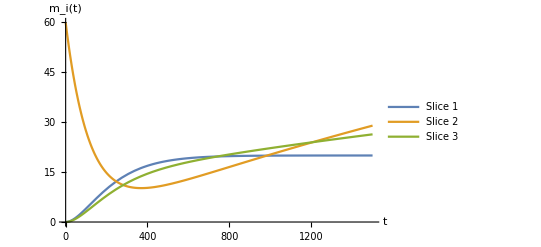

```mathematica
Plot[{Subscript[H, 1][t],Subscript[H, 2][t],Subscript[H, 3][t]},{t,0,1500}, 
PlotRange->All,
PlotLegends->Placed[{"Slice 1","Slice 2","Slice 3"},Right],
AxesLabel->{t,m_i[t]}]
```

```mathematica
N[Subscript[H, 1][x]]
```

2.02448×10^-12 2.71828^(-0.0333333 x) (-3.21148×10^13 2.71828^(0.025 x)+1.04486×10^13 2.71828^(0.0331019 x)+7. (3.09518×10^12+6.52862×10^10 x+6.15924×10^8 x^2+2.92421×10^6 x^3))+20. (1.+0.0902998 2.71828^(-0.00833333 x)-1.05765 2.71828^(-0.000231481 x)-4.92062×10^-15 2.71828^(-0.0333333 x) (6.63615×10^12+1.18032×10^11 x+8.79103×10^8 x^2+2.92421×10^6 x^3))

```mathematica
FindRoot[Subscript[H, 1][x]-0.95*20,{x,1}]
FindRoot[Subscript[H, 2][x]-0.95*100,{x,1000}]
FindRoot[Subscript[H, 3][x]-0.95*60,{x,1000}]
```

{x→569.264}

{x→12963.4}

{x→11433.4}

### RNDM 2022: Phased recovery after massive failure - three stages - stage 1 non-exponential

```mathematica
(* Stage 1: disaster hits, (emergency)slices 1 and 3 down, no rerouting possible, while(non-emegency) slice 2 is rerouted - stage duation is Erl-4(4 Subscript[μ, 2]) distributed *)
(* Stage 2: Disaster escalation - all slices / flows disconnected *)
(* Stage 3: emergency slices 1 and 3 recovered (a router and links in the disaster is partly recovered), while(non-emegency) slice 2 is still rerouted, but will be reduced to make space for 1+3. *)
(*(eq={
D[Subscript[p, 1][t],t]== -Subscript[μ, 1] Subscript[p, 1][t],
D[Subscript[p, 21][t],t]==-Subscript[μ, 2] Subscript[p, 21][t]+Subscript[μ, 1] Subscript[p, 1][t],
D[Subscript[p, 22][t],t]==-Subscript[μ, 2] Subscript[p, 22][t]+Subscript[μ, 2] Subscript[p, 21][t],
D[Subscript[p, 23][t],t]==-Subscript[μ, 2] Subscript[p, 23][t]+Subscript[μ, 2] Subscript[p, 22][t],
D[Subscript[p, 24][t],t]==-Subscript[μ, 2] Subscript[p, 24][t]+Subscript[μ, 2] Subscript[p, 23][t],
D[Subscript[p, 3][t],t]==-Subscript[μ, 3] Subscript[p, 3][t]+Subscript[μ, 2] Subscript[p, 24][t],
D[Subscript[p, 0][t],t]==Subscript[μ, 3] Subscript[p, 3][t] 
});  *)(*// MatrixForm *)
(* Erlang-k for phase 1-3 (k<10) *)
Subscript[k, 1]=3;
Subscript[k, 2]=0;
Subscript[k, 3]=3;
eq={Subscript[p, 10]'[t]== -Subscript[μ, 1] Subscript[p, 10][t]};
AppendTo[eq,Subscript[p, 10+#+1]'[t]== -Subscript[μ, 1] Subscript[p, 10+#+1][t]+Subscript[μ, 1] Subscript[p, 10+#][t]&/@Range[0,Subscript[k, 1]-1]];
AppendTo[eq,Subscript[p, 20]'[t]==Subscript[μ, 1] Subscript[p, 10+Subscript[k, 1]][t]-Subscript[μ, 2] Subscript[p, 20][t]];
AppendTo[eq,Subscript[p, 20+#+1]'[t]== -Subscript[μ, 2] Subscript[p, 20+#+1][t]+Subscript[μ, 2] Subscript[p, 20+#][t]&/@Range[0,Subscript[k, 2]-1]];
AppendTo[eq,Subscript[p, 30]'[t]==Subscript[μ, 2] Subscript[p, 20+Subscript[k, 2]][t]-Subscript[μ, 3] Subscript[p, 30][t]];
AppendTo[eq,Subscript[p, 30+#+1]'[t]== -Subscript[μ, 3] Subscript[p, 30+#+1][t]+Subscript[μ, 3] Subscript[p, 30+#][t]&/@Range[0,Subscript[k, 3]-1]];
AppendTo[eq,Subscript[p, 0]'[t]==Subscript[μ, 3] Subscript[p, 30+Subscript[k, 3]][t]];
eq = Flatten[eq];
eq //MatrixForm
(*init = {Subscript[p, 1][0]==1,Subscript[p, 21][0]==0,Subscript[p, 22][0]==0,Subscript[p, 23][0]==0,Subscript[p, 24][0]==0,Subscript[p, 3][0]==0,Subscript[p, 0][0]==0};*)
init ={Subscript[p, 10][0]==1,(Subscript[p, 10+#][0]==0)&/@Range[1,Subscript[k, 1]],(Subscript[p, 20+#][0]==0)&/@Range[0,Subscript[k, 2]],(Subscript[p, 30+#][0]==0)&/@Range[0,Subscript[k, 3]],Subscript[p, 0][0]==0} //Flatten;
(*init = Flatten[{Subscript[p, 1][0]==1,(Subscript[p, #][0]==0)&/@Range[21,24],Subscript[p, 30][0]==0,Subscript[p, 0][0]==0}];*)
(*vars = {Subscript[p, 1][t],Subscript[p, 21][t],Subscript[p, 22][t],Subscript[p, 23][t],Subscript[p, 24][t],Subscript[p, 3][t],Subscript[p, 0][t]};*)
(*vars = Flatten[{Subscript[p, 1][t],Subscript[p, #][t]&/@Range[21,24],Subscript[p, 30][t],Subscript[p, 0][t]}];*)
vars = {Subscript[p, 10+#][t]&/@Range[0,Subscript[k, 1]],Subscript[p, 20+#][t]&/@Range[0,Subscript[k, 2]],Subscript[p, 30+#][t]&/@Range[0,Subscript[k, 3]],Subscript[p, 0][t]} //Flatten;
(* Parameters: rates = 1/expected duration of stages *)
(* First stage 2 hours(120 min), and second (escalation) 2 hours (120 min), and third 3 days (4320 min)*)
para={Subscript[μ, 1]->(Subscript[k, 1]+1)/120,Subscript[μ, 2]->(Subscript[k, 2]+1)/240,Subscript[μ, 3]->(Subscript[k, 3]+1)/4320};
(* Reward (bit rate) *)
(* Emergency : 20 Mbps (pri 1) *)
(* Non-emergency : 120 Mbps (pri 3) - drop to 5 in recovery - rerouted and change of *)  
(* Emergency : 60 Mbps (pri 2) - drop to 10 in recovery *) 
Subscript[m, 1] = {20,0,0,20};
Subscript[m, 2] = {100,60,0,5};
Subscript[m, 3] = {60,0,0,15};
(* Solve *)
sol=DSolve[Flatten[{(eq /.para),init}],vars,t] //Simplify;
(*Do[Subscript[f, i][t_] = Subscript[p, i][t] /. sol[[1]],{i,0,3}];*)
Subscript[f, 0][t_] = Subscript[p, 0][t] /. sol[[1]];
Subscript[f, 1][t_]= Apply[Plus,(Subscript[p, 10+#][t] /. sol[[1]])&/@Range[0,Subscript[k, 1]]];
Subscript[f, 2][t_]= Apply[Plus,(Subscript[p, 20+#][t] /. sol[[1]])&/@Range[0,Subscript[k, 2]]];
Subscript[f, 3][t_]= Apply[Plus,(Subscript[p, 30+#][t] /. sol[[1]])&/@Range[0,Subscript[k, 3]]];
F[t_]:=Table[Subscript[f, i][t],{i,0,3}];
(* Plot rewards for each i=1,2,3 *)
(Subscript[H, #][t_]:= F[t].Subscript[m, #] /. para)&/@ Range[3];
(Subscript[G, #][t_]:= F[t][[#+1]] /. para)&/@ Range[0,3];
```

(p_10'[t]==-μ_1 p_10[t]
p_11'[t]==μ_1 p_10[t]-μ_1 p_11[t]
p_12'[t]==μ_1 p_11[t]-μ_1 p_12[t]
p_13'[t]==μ_1 p_12[t]-μ_1 p_13[t]
p_20'[t]==μ_1 p_13[t]-μ_2 p_20[t]
p_30'[t]==μ_2 p_20[t]-μ_3 p_30[t]
p_31'[t]==μ_3 p_30[t]-μ_3 p_31[t]
p_32'[t]==μ_3 p_31[t]-μ_3 p_32[t]
p_33'[t]==μ_3 p_32[t]-μ_3 p_33[t]
p_0'[t]==μ_3 p_33[t])

```mathematica
(Subscript[X, #][t_]:=If[t<0,Subscript[m, #][[1]],Subscript[H, #][t]]) & /@ Range[3];
```

```mathematica
Subscript[X, 1][100] //N
```

1.02535

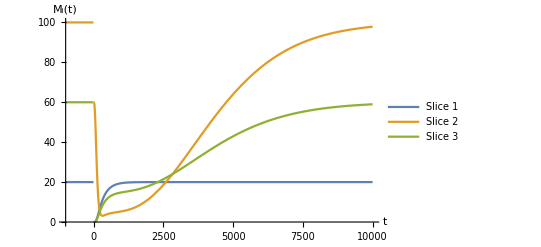

```mathematica
Plot[{Subscript[X, 1][t],Subscript[X, 2][t],Subscript[X, 3][t]},{t,-1000,10000}, 
PlotRange->All,
PlotLegends->Placed[{"Slice 1","Slice 2","Slice 3"},Top],
AxesLabel->{t,Subscript[M, i][t]}, AxesOrigin->{-1000,0}]
```

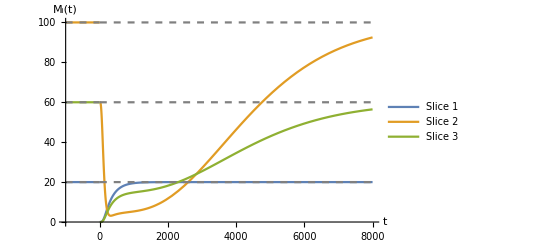

```mathematica
Plot[{Subscript[X, 1][t],Subscript[X, 2][t],Subscript[X, 3][t],Subscript[m, 1][[1]],Subscript[m, 2][[1]],Subscript[m, 3][[1]]},{t,-1000,8000}, 
PlotRange->All,
PlotStyle->{Automatic,Automatic,Automatic, 
Directive[Gray,Dashed], Directive[Gray,Dashed], Directive[Gray,Dashed]},
PlotLegends->Placed[{"Slice 1","Slice 2","Slice 3"},Top],
AxesLabel->{t,Subscript[M, i][t]}, AxesOrigin->{-1000,0}]
```

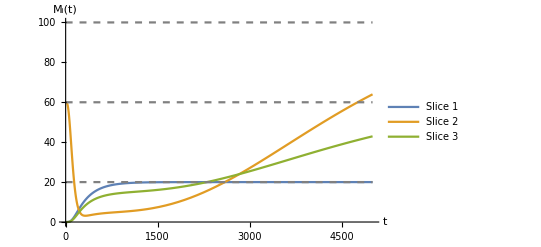

```mathematica
Plot[{Subscript[H, 1][t],Subscript[H, 2][t],Subscript[H, 3][t],Subscript[m, 1][[1]],Subscript[m, 2][[1]],Subscript[m, 3][[1]]},{t,0,5000}, 
PlotRange->All,
PlotStyle->{Automatic,Automatic,Automatic, 
Directive[Gray,Dashed], Directive[Gray,Dashed], Directive[Gray,Dashed]},
PlotLegends->Placed[{"Slice 1","Slice 2","Slice 3"},Top],
AxesLabel->{t,Subscript[M, i][t]}]
```

### ITC 2020 : Phased recovery after massive failure

```mathematica
(eq={
D[Subscript[p, 1][t],t]== -Subscript[μ, 1] Subscript[p, 1][t],
D[Subscript[p, 2][t],t]==-Subscript[μ, 2] Subscript[p, 2][t]+Subscript[μ, 1] Subscript[p, 1][t],
D[Subscript[p, 3][t],t]==-Subscript[μ, 3] Subscript[p, 3][t]+Subscript[μ, 2] Subscript[p, 2][t],
D[Subscript[p, 4][t],t]==-Subscript[μ, 4] Subscript[p, 4][t]+Subscript[μ, 3] Subscript[p, 3][t],
D[Subscript[p, 5][t],t]==-Subscript[μ, 5] Subscript[p, 5][t]+Subscript[μ, 4] Subscript[p, 4][t], 
D[Subscript[p, 0][t],t]==Subscript[μ, 5] Subscript[p, 5][t] 
});  (*// MatrixForm *)
init = {Subscript[p, 1][0]==1,Subscript[p, 2][0]==0,Subscript[p, 3][0]==0,Subscript[p, 4][0]==0,Subscript[p, 5][0]==0,Subscript[p, 0][0]==0};
vars = {Subscript[p, 1][t],Subscript[p, 2][t],Subscript[p, 3][t],Subscript[p, 4][t],Subscript[p, 5][t],Subscript[p, 0][t]};
```

```mathematica
R = {1,0.1,0.35,0.4,0.4,0.65};
para={Subscript[μ, 1]-> 0.1,Subscript[μ, 2]-> 0.001,Subscript[μ, 3]-> 0.1,Subscript[μ, 4]-> 0.001,Subscript[μ, 5]-> 0.1};
```

```mathematica
sol=DSolve[Flatten[{(eq /.para),init}],vars,t] //Simplify
Do[Subscript[f, i][t_] = Subscript[p, i][t] /. sol[[1]],{i,0,5}];
F[t_]:=Table[Subscript[f, i][t],{i,0,5}];
H[t_]:= F[t].R /. para
Apply[Plus,(F[100] /. para)]
```

{{p_0[t]→1.+ⅇ^(-0.001 t) (-0.99938-0.00103061 t)+ⅇ^(-0.1 t) (-0.000620459-0.0000308152 t-5.10152×10^-7 t^2),p_1[t]→1.10776×10^-16 ⅇ^(-0.001 t)+ⅇ^(-0.1 t) (1.-2.7618×10^-19 t),p_2[t]→-1.0101 ⅇ^(-0.1 t)+ⅇ^(-0.001 t) (1.0101+2.18172×10^-17 t),p_3[t]→0.010203 ⅇ^(-0.001 t)+ⅇ^(-0.1 t) (-0.010203-0.0010101 t),p_4[t]→ⅇ^(-0.001 t) (-0.0206122+0.0010203 t)+ⅇ^(-0.1 t) (0.0206122+0.0010203 t),p_5[t]→ⅇ^(-0.001 t) (-0.000312306+0.0000103061 t)+ⅇ^(-0.1 t) (0.000312306+0.0000206122 t+5.10152×10^-7 t^2)}}

1.

```mathematica
FindRoot[H[u]-0.35,{u,0.1}]
```

{u→47.9065}

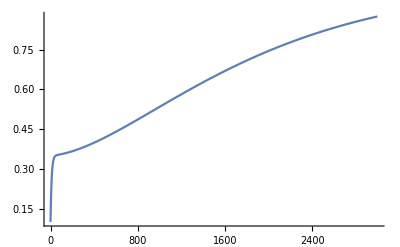

```mathematica
Plot[(F[t].R /. para),{t,0,3000}, PlotRange->All]
```

### Phased recovery after massive failure with secondary effect

```mathematica
(eq={
D[Subscript[p, 1][t],t]== -Subscript[μ, 1] Subscript[p, 1][t],
D[Subscript[p, 2][t],t]==-Subscript[μ, 2] Subscript[p, 2][t]+Subscript[μ, 1] Subscript[p, 1][t],
D[Subscript[p, 3][t],t]==-Subscript[μ, 3] Subscript[p, 3][t]+Subscript[μ, 2] Subscript[p, 2][t],
D[Subscript[p, 4][t],t]==-Subscript[μ, 4] Subscript[p, 4][t]+Subscript[μ, 3] Subscript[p, 3][t],
D[Subscript[p, 5][t],t]==-Subscript[μ, 5] Subscript[p, 5][t]+Subscript[μ, 4] Subscript[p, 4][t], 
D[Subscript[p, 0][t],t]==Subscript[μ, 5] Subscript[p, 5][t] 
});  (*// MatrixForm *)
init = {Subscript[p, 1][0]==1,Subscript[p, 2][0]==0,Subscript[p, 3][0]==0,Subscript[p, 4][0]==0,Subscript[p, 5][0]==0,Subscript[p, 0][0]==0};
vars = {Subscript[p, 1][t],Subscript[p, 2][t],Subscript[p, 3][t],Subscript[p, 4][t],Subscript[p, 5][t],Subscript[p, 0][t]};
```

```mathematica
R = {1,0.1,0.35,0.4,0.4,0.65};
para={Subscript[μ, 1]-> 0.1,Subscript[μ, 2]-> 0.001,Subscript[μ, 3]-> 0.1,Subscript[μ, 4]-> 0.001,Subscript[μ, 5]-> 0.1};
```

```mathematica
sol=DSolve[Flatten[{(eq /.para),init}],vars,t] //Simplify
Do[Subscript[f, i][t_] = Subscript[p, i][t] /. sol[[1]],{i,0,5}];
F[t_]:=Table[Subscript[f, i][t],{i,0,5}];
H[t_]:= F[t].R /. para
```

{{p_0[t]→1.+ⅇ^(-0.001 t) (-0.99938-0.00103061 t)+ⅇ^(-0.1 t) (-0.000620459-0.0000308152 t-5.10152×10^-7 t^2),p_1[t]→1.10776×10^-16 ⅇ^(-0.001 t)+ⅇ^(-0.1 t) (1.-2.7618×10^-19 t),p_2[t]→-1.0101 ⅇ^(-0.1 t)+ⅇ^(-0.001 t) (1.0101+2.18172×10^-17 t),p_3[t]→0.010203 ⅇ^(-0.001 t)+ⅇ^(-0.1 t) (-0.010203-0.0010101 t),p_4[t]→ⅇ^(-0.001 t) (-0.0206122+0.0010203 t)+ⅇ^(-0.1 t) (0.0206122+0.0010203 t),p_5[t]→ⅇ^(-0.001 t) (-0.000312306+0.0000103061 t)+ⅇ^(-0.1 t) (0.000312306+0.0000206122 t+5.10152×10^-7 t^2)}}

### BCMP network (generalization of Jackson network)

F. Baskett, K. M. Chandy, R. R. Muntz, and F. G. Palacios, “Open, closed, and mixed networks of queues with different
classes of customers,” J. ACM, vol. 22, no. 2, pp. 248–260, 1975.

```mathematica
(* Traffic intensity per path from cache(s) to the users *)
λtab = {Subscript[λ, 1],Subscript[λ, 2],Subscript[λ, 3],Subscript[p, 4] Subscript[λ, 4],(1-Subscript[p, 4])Subscript[λ, 4],Subscript[λ, 5]};
tabC = Table[1,{Length[λtab]}];
(* Service rate for each of the nodes *)
μtab ={Subscript[μ, 1],Subscript[μ, 2],Subscript[μ, 3],Subscript[μ, 4],Subscript[μ, 5],Subscript[μ, 6], Subscript[μ, 7], Subscript[μ, 8], Subscript[μ, 9], Subscript[μ, 10] ,Subscript[μ, 11]};
tabK = Table[1,{Length[μtab]}];
```

```mathematica
(* Routing of paths from cache to user *)
(Itab =
 {
{1,1,0,0,0,0,0,0,0,0,0,0},
{1,1,1,0,0,0,0,0,0,0,0,0},
{1,0,1,1,0,0,0,1,1,0,0,0},
{1,0,0,1,0,0,0,0,0,0,0,0},
{1,0,0,0,0,0,0,0,1,0,0,0},
{1,0,0,0,0,0,0,0,0,0,1,1}
} )//MatrixForm;
```

```mathematica
(Λtab = Drop[λtab . Itab,1]) //MatrixForm
```

(λ_1+λ_2
λ_2+p_3 λ_3
(1-p_3) λ_3+p_3 λ_3
0
0
0
p_3 λ_3
p_3 λ_3+λ_4
0
λ_5
λ_5)

```mathematica
EN = (Λtab / (μtab - Λtab)) . tabK;
EW = EN /(Take[λtab . Itab,1])
```

{((λ_1+λ_2)/(-λ_1-λ_2+μ_1)+(λ_2+p_3 λ_3)/(-λ_2-p_3 λ_3+μ_2)+(p_3 λ_3+λ_5)/(-p_3 λ_3-λ_5+μ_3)+(p_3 λ_3)/(-p_3 λ_3+μ_7)+((1-p_3) λ_3+p_3 λ_3)/(-(1-p_3) λ_3-p_3 λ_3+μ_8)+λ_4/(-λ_4+μ_10)+λ_4/(-λ_4+μ_11))/(λ_1+λ_2+(1-p_3) λ_3+p_3 λ_3+λ_4+λ_5)}

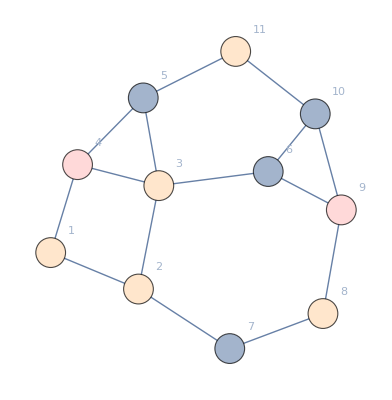

```mathematica
(* Plot network example *)
Subscript[V, G]=Table[i,{i,11}];
Subscript[L, G]={1<-> 2,1<-> 4,2<-> 3,2<-> 7,3<-> 4,3<-> 5,3<-> 6,4<-> 5,5<-> 11,6<-> 9,6<-> 10,7<-> 8,8<-> 9,9<-> 10,10<-> 11};
Subscript[G, G] = Graph[Subscript[V, G],Subscript[L, G],VertexLabels->Table[i-> i,{i,11}],VertexSize->Large];
Subscript[G, HC]= HighlightGraph[Subscript[G, G],{{1,2,3,8,11,4,9},Style[{1,2,3,8,11},LightOrange],Style[{4,9},LightRed]}]
```

```mathematica
CityData["Gøteborg", "Population"]
```

515252 people